```mathematica
Clear[TMax,f,dF,t,y]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:={y2,y3,-a*y3+b*y2-c*(y2)^3-y1}
p={a,b,c}={.6,2.8,1};y0={0,1,0};TMax=287.75;
ySol=NDSolveValue[ {y'[t]==f[p][y[t]], y[0]==y0},y,{t,0, TMax}];
ParametricPlot3D[ySol[t],{t,.8*TMax,TMax},PlotLabel->"Phase Plot - Once Around",PlotLegends->{"y","y'","y''"},AxesLabel->{"y","y'","y''"},PlotRange->All,PlotPoints->100]
```

-Graphics3D-

```mathematica
Plot[ySol[t],{t,0.8 TMax,TMax}];
```

InterpolatingFunction[{{0., 287.75}}, <>]

-Graphics3D-

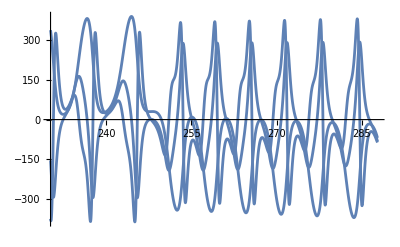

-Graphics3D-

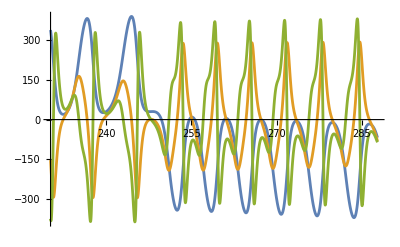

```mathematica
{y1sol,y2sol,y3sol}=NDSolveValue[{y1'[t]==y2[t],y2'[t]==y3[t],y3'[t]==-a*y3[t]+b*y2[t]-c*y2[t]^3-y1[t],y1[0]==0,y2[0]==1,y3[0]==0},{y1,y2,y3},{t,0,TMax}];

ParametricPlot3D[{y1sol[t],y2sol[t],y3sol[t]},{t,.8*TMax,TMax},PlotLabel->"Phase Plot - Once Around",PlotLegends->{"y","y'","y''"},AxesLabel->{"y","y'","y''"},PlotRange->All,PlotPoints->100]
Plot[{y1sol[t],y2sol[t],y3sol[t]},{t,0.8 TMax,TMax}]
```